```mathematica
ints=Flatten[Import["10k-ints.txt","Table"]]
```

{92456957836725077,75649505469473047,91695452451713563,99365237515560343,86505388710929656,85160388841586148,2459151629361831,«9986»,65705442657723439,46009534376750542,42086808797812492,6782228693372245,93121443236533640,16773207853017940,79772565722852700}

```mathematica
fracs=#/(10^17)&/@ints
```

{92456957836725077/100000000000000000,75649505469473047/100000000000000000,91695452451713563/100000000000000000,99365237515560343/100000000000000000,«9993»,2328036080913341/2500000000000000,838660392650897/5000000000000000,797725657228527/1000000000000000}

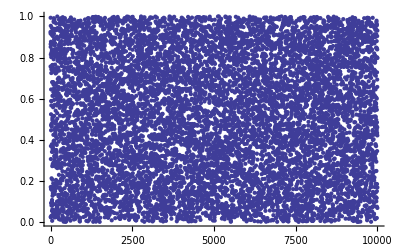

```mathematica
ListPlot[fracs]
```

```mathematica
freqs=Table[Pi 2^n,{n,1,55}]
```

{2 π,4 π,8 π,16 π,32 π,64 π,128 π,256 π,512 π,1024 π,2048 π,4096 π,8192 π,16384 π,32768 π,65536 π,131072 π,262144 π,524288 π,1048576 π,2097152 π,4194304 π,8388608 π,16777216 π,33554432 π,67108864 π,134217728 π,268435456 π,536870912 π,1073741824 π,2147483648 π,4294967296 π,8589934592 π,17179869184 π,34359738368 π,68719476736 π,137438953472 π,274877906944 π,549755813888 π,1099511627776 π,2199023255552 π,4398046511104 π,8796093022208 π,17592186044416 π,35184372088832 π,70368744177664 π,140737488355328 π,281474976710656 π,562949953421312 π,1125899906842624 π,2251799813685248 π,4503599627370496 π,9007199254740992 π,18014398509481984 π,36028797018963968 π}

sins[[i]] is samples from Sin[2^i π x] it begins to look unrelated very fast

```mathematica
sins=Map[Function[freq,Map[{#,N[Sin[freq #],20]}&,Take[fracs,1000]]],freqs];
```

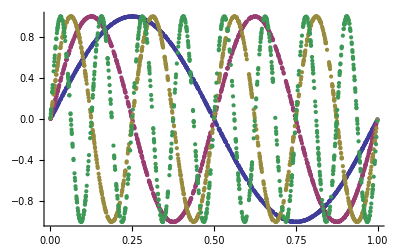

```mathematica
ListPlot[sins[[{1,2,3,4}]]]
```

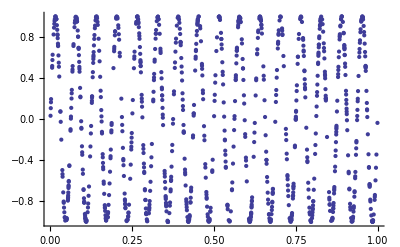

```mathematica
ListPlot[sins[[{5}]]]
```

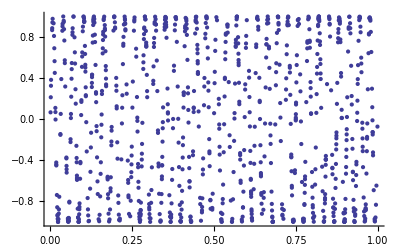

```mathematica
ListPlot[sins[[6]]]
```

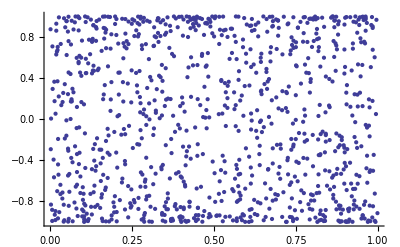

```mathematica
ListPlot[sins[[10]]]
```

```mathematica
freqs[[{1,2,3,4,5,6,10}]]
```

{2 π,4 π,8 π,16 π,32 π,64 π,1024 π}